```mathematica
L[f_]:=((R0 + ((2 * (f-f0))/dW)^2)/(1 + ((2 * (f-f0))/dW)^2));
```

```mathematica
R0 = 0.8; f0 = 2900; dW = 10;
```

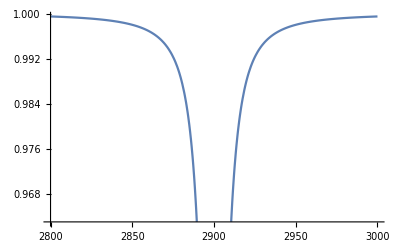

```mathematica
Plot[L[f], {f, 2880, 3300}]
```

```mathematica
Clear[R0, f0, dw];
FullSimplify[L[f]]
```

(4 (f-f0)^2+dW^2 R0)/(dW^2+4 (f-f0)^2)